## FindShortestPath

## Basic Examples

Find a shortest path between two individual vertices in a graph:

```mathematica
g=-Graphics-;
```

```mathematica
FindShortestPath[g,3,5]
```

{3,1,5}

```mathematica
HighlightGraph[,PathGraph[{3,1,5}]]
```

-Graphics-

## Options

### Method

The method is automatically chosen depending on the input:

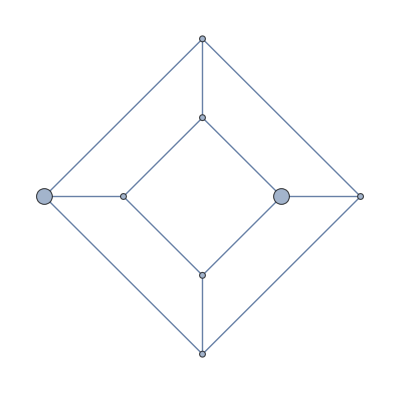
{-Graphics-,-Graphics-}

```mathematica
{PetersenGraph[4,1,VertexSize->{1->Medium,7->Medium}],PetersenGraph[4,1,EdgeWeight->{4,0,3,1,3,2,7,8,5,2,1,6},VertexSize->{1->Medium,7->Medium}]}
```

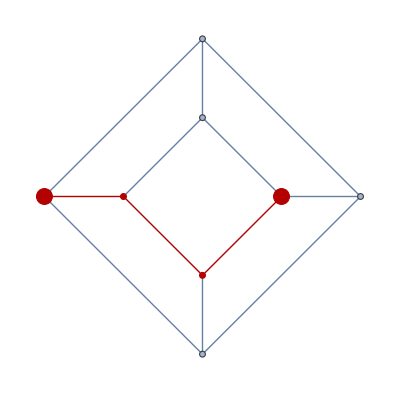
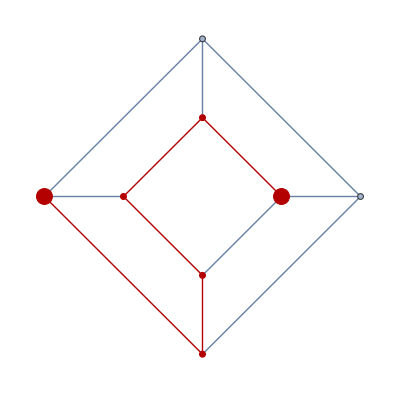

```mathematica
Table[HighlightGraph[g,PathGraph@FindShortestPath[g,1,7]],{g,}]
```

“UnitWeight” method will use the weight 1 for every edge:

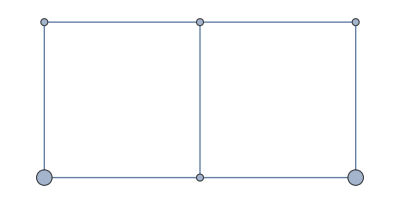

```mathematica
GridGraph[{2,3},EdgeWeight->{5,2,2,5,1,2,2},VertexSize->{1->Small,5->Small}]
```

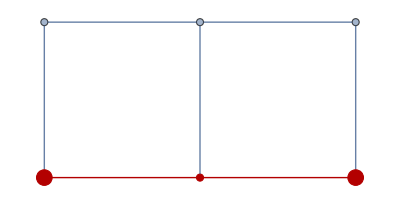

```mathematica
HighlightGraph[,PathGraph@FindShortestPath[,1,5,Method->"UnitWeight"]]
```

“Dijkstra” can be used for graphs with positive edge weights only:

```mathematica
GridGraph[{2,3},EdgeWeight->{5,2,2,5,1,2,2},VertexSize->{1->Small,5->Small}]
```

-Graphics-

```mathematica
HighlightGraph[,PathGraph@FindShortestPath[,1,5,Method->"Dijkstra"]]
```

-Graphics-

### Properties and Relations

The distance between two vertices can be found using the shortest path:

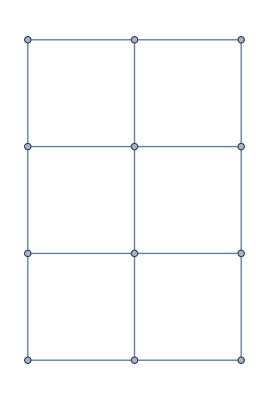

```mathematica
g=GridGraph[{4,3}]
```

```mathematica
FindShortestPath[,1,12]
```

{1,2,3,4,8,12}

```mathematica
Length[]-1
```

5

```mathematica
GraphDistance[g,1,12]
```

5

## ShortestPathFunction

## Basic Examples

Obtain a function that gives shortest paths from vertex 4:

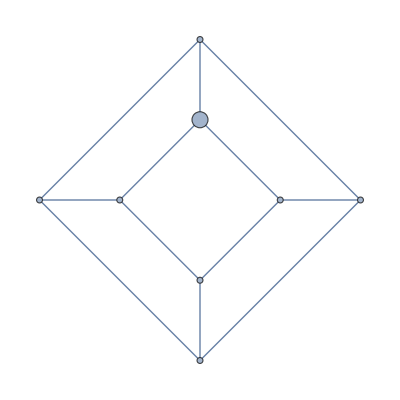

```mathematica
g=PetersenGraph[4,1,VertexSize->{4->Medium}]
```

```mathematica
spf=FindShortestPath[g,4,All]
```

ShortestPathFunction[{4,All},«»]

Use it to show the shortest paths to all vertices:

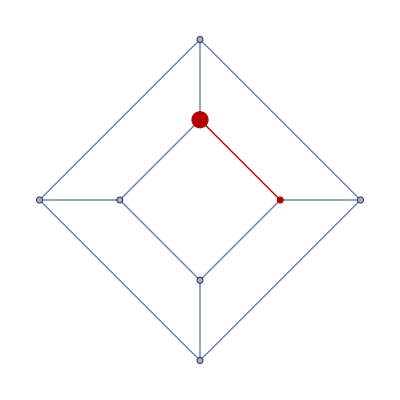
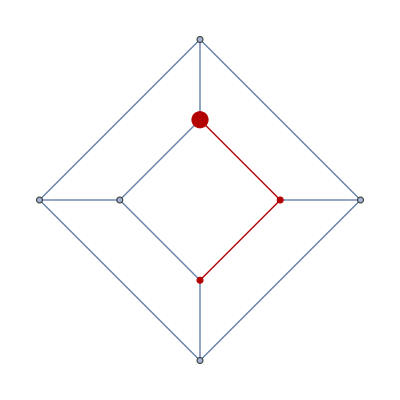
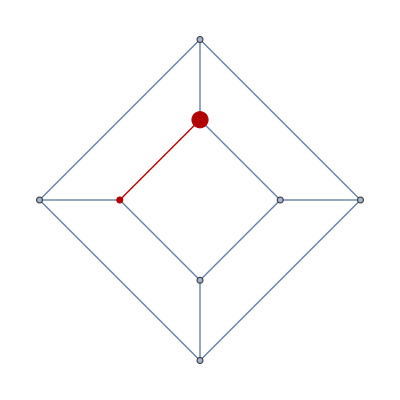
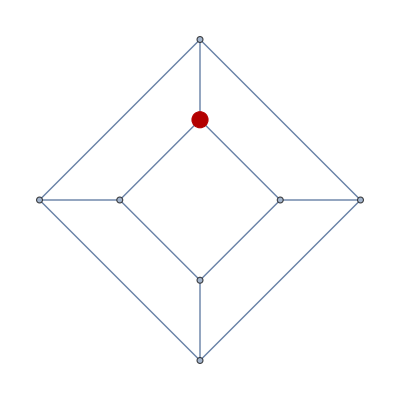
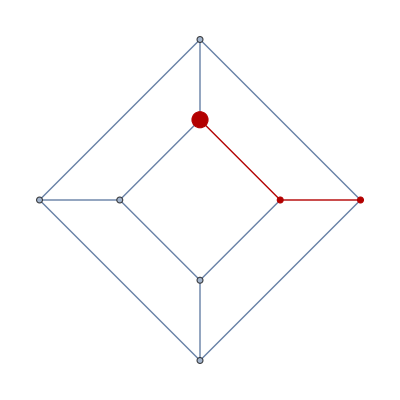
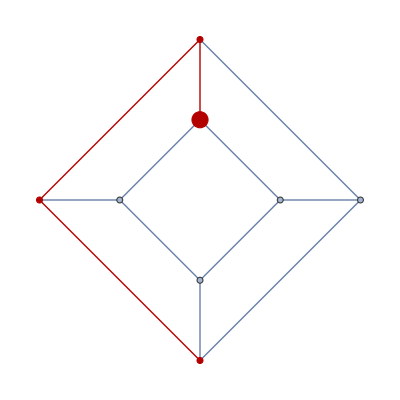
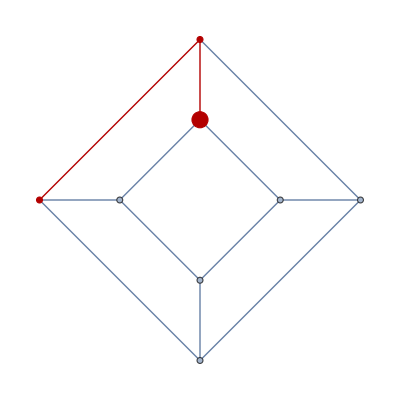
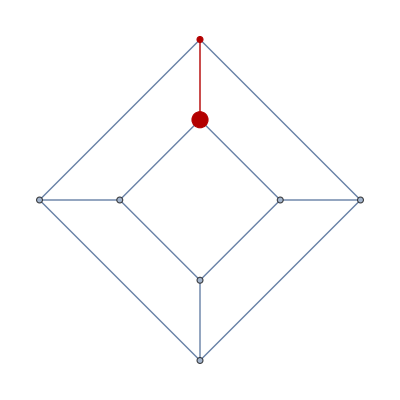

```mathematica
Table[HighlightGraph[g,PathGraph[spf[v]]],{v,VertexList[g]}]
```

## FindHamiltonianPath

## Basic Examples

Find a Hamiltonian path through vertices in a graph:

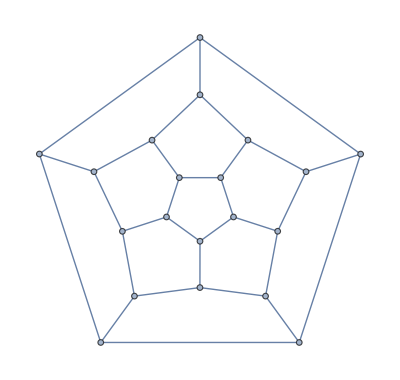

```mathematica
g=PolyhedronData["Dodecahedron","Skeleton"]
```

```mathematica
FindHamiltonianPath[g]
```

{13,18,10,15,4,20,6,2,5,19,3,7,11,12,8,16,1,14,9,17}

Highlight the path:

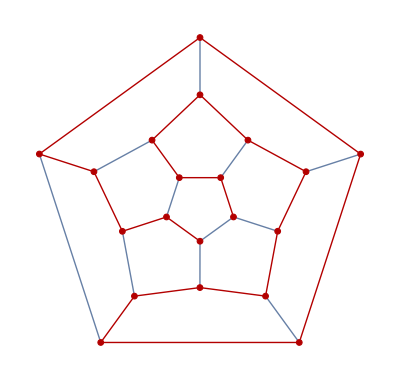

```mathematica
HighlightGraph[g,PathGraph[]]
```

Find a Hamiltonian path between two individual vertices in a graph:

```mathematica
g=PolyhedronData["Dodecahedron","Skeleton"]
```

-Graphics-

```mathematica
FindHamiltonianPath[g,1,5]
```

{1,15,10,18,20,4,8,16,7,11,12,6,2,13,17,9,14,3,19,5}

Highlight the path:

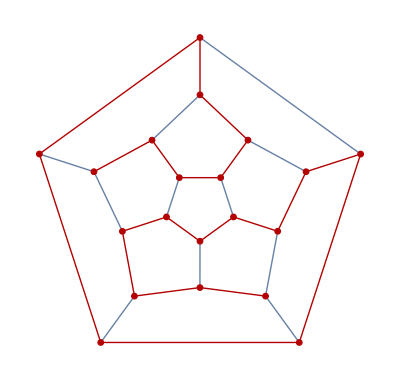

```mathematica
HighlightGraph[g,PathGraph[]]
```

## Options

### DistanceFunction

This defines a sparse distance matrix among six points:

```mathematica
d=SparseArray[{{1,2}->2,{2,1}->1,{6,1}->1,{6,2}->2,{5,1}->1,{1,5}->1,{5,3}->1,{3,4}->1,{4,3}->1,{4,5}->15,{4,1}->1,{5,4}->15,{5,2}->2,{1,4}->1,{2,5}->1,{1,6}->1},{6,6},Infinity]
```

SparseArray[…]

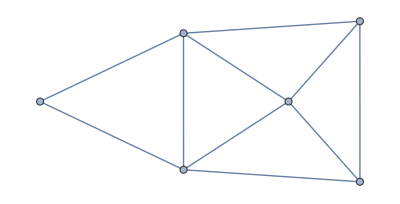
```mathematica
g=-Graphics-;
```

Find a Hamiltonian path:

```mathematica
path=FindHamiltonianPath[g,DistanceFunction->(d[[#1,#2]]&)]
```

{6,1,2,5,4,3}

Highlight the path:

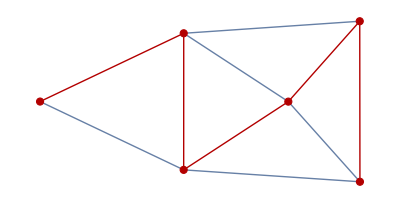

```mathematica
HighlightGraph[g,PathGraph[path]]
```

## Applications

Find a squence of moves by a knight chess piece that visits each square of an 8x8 chessboard exactly once:

```mathematica
g=KnightTourGraph[8,8];
```

```mathematica
path=FindHamiltonianPath[g]
```

{64,47,30,40,55,38,53,36,51,57,42,27,17,2,12,6,16,31,48,54,37,52,35,50,33,18,1,11,5,20,26,41,58,43,60,45,62,56,39,29,23,8,14,24,7,13,3,9,19,25,10,4,21,15,32,22,28,34,49,59,44,61,46,63}

A knight’s move:

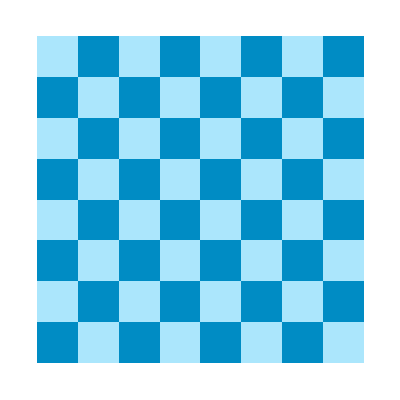

```mathematica
checkerboard=ArrayPlot[Table[Mod[j+i,2],{i,8},{j,8}],ColorRules->{1->RGBColor[0,.55,.77],0->RGBColor[.67,.9,.99]},Frame->False,DataRange->{{1,8},{1,8}}]
```

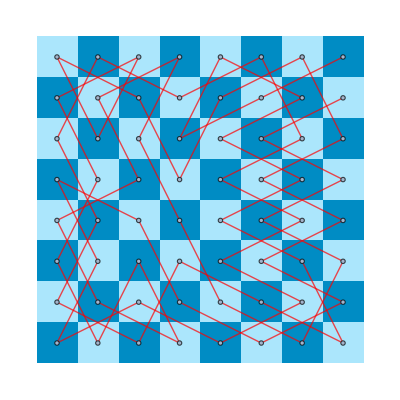

```mathematica
Show[checkerboard,HighlightGraph[g,PathGraph[path],GraphHighlightStyle->"DehighlightHide",EdgeStyle->Directive[Thick,Red]]]
```

## FindMaximumFlow

## Basic Examples

Find the maximum flow between two vertices in a graph.

```mathematica
FindMaximumFlow[-Graphics-,1,4]
```

2

```mathematica
ℱ=FindMaximumFlow[-Graphics-,"s","t","OptimumFlowData"];
```

```mathematica
ℱ["FlowValue"]
```

3

```mathematica
ℱ["FlowGraph"]
```

-Graphics-

## Options

### EdgeCapacity

By default, the edge capacity of an edge is taken to be its EdgeCapacity property if available, otherwise 1:

```mathematica
FindMaximumFlow[-Graphics-,1,2]
```

2

Use EdgeCapacity->capacities to set the edge capacity:

```mathematica
FindMaximumFlow[-Graphics-,1,2,EdgeCapacity->Range[5]]
```

3

### VertexCapacity

By default, the vertex capacity of a vertex is taken to be its VertexaCapacity property if available, otherwise Infinity:

```mathematica
FindMaximumFlow[-Graphics-,1,4]
```

2

Use VertexCapacity->capacities to set the vertex capacity:

```mathematica
FindMaximumFlow[-Graphics-,1,4,VertexCapacity->Range[4]]
```

1

## Properties and Relations

The sum of in-flows is equal to the sum of out-flows for interior vertices:

```mathematica
ℱ=FindMaximumFlow[-Graphics-,1,6,"OptimumFlowData"];
```

```mathematica
(m=ℱ["FlowMatrix"])//MatrixForm
```

(0 | 6 | 0 | 0 | 0 | 0
0 | 0 | 3 | 4 | 0 | 0
0 | 1 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0)

The in-flow for interior vertices:

```mathematica
Table[Total[m[[All,i]]],{i,2,5}]
```

{7,3,4,2}

The out-flow for interior vertices:

```mathematica
Table[Total[m[[i,All]]],{i,2,5}]
```

{7,3,4,2}

A graph with self-loops is treated as a simple graph:

```mathematica
g=-Graphics-;
```

```mathematica
FindMaximumFlow[g,1,5]
```

2

```mathematica
FindMaximumFlow[SimpleGraph[g],1,5]
```

2

The edge connectivity between two vertices is equal to the value of the maximum flow:

```mathematica
g=-Graphics-;
```

```mathematica
FindMaximumFlow[g,1,7]
```

3

```mathematica
EdgeConnectivity[g,1,7]
```

3

The vertex connectivity can be found using FindMaximumFlow:

```mathematica
g=-Graphics-;
```

```mathematica
VertexConnectivity[g,1,4]
```

```mathematica
FindMaximumFlow[g,1,4,VertexCapacity->{EdgeCount[g],1,1,EdgeCount[g]}]
```

1

## FindMinimumCostFlow

## Basic Examples

Find the minimum cost flow between supply and demand:

```mathematica
FindMinimumCostFlow[-Graphics-,{1,3,4,-3,-4,-1}]
```

8

Find the minimum cost maximum flow between two vertices in a graph:

```mathematica
ℱ=FindMinimumCostFlow[-Graphics-,"s","t","OptimumFlowData"];
```

```mathematica
ℱ["CostValue"]
```

9

Highlight the flow:

```mathematica
ℱ["FlowGraph"]
```

-Graphics-

## OptimumFlowData

## Basic Examples

Create an OptimumFlowData object using FindMaximumFlow:

```mathematica
ℱ=FindMaximumFlow[-Graphics-,1,4, "OptimumFlowData"]
```

OptimumFlowData[…]

Obtain a list of properties:

```mathematica
ℱ["Properties"]
```

{CostValue,EdgeList,FlowGraph,FlowMatrix,FlowTable,FlowValue,Properties,ResidualGraph,VertexList}

Extract a property:

```mathematica
ℱ["FlowValue"]
```

2

## GraphDistance

## Basic Examples

Give the distance for a grid graph:

```mathematica
GraphDistance[-Graphics-,1,6]
```

3

## Options

### Method

The method is automatically chosen, depending on input:

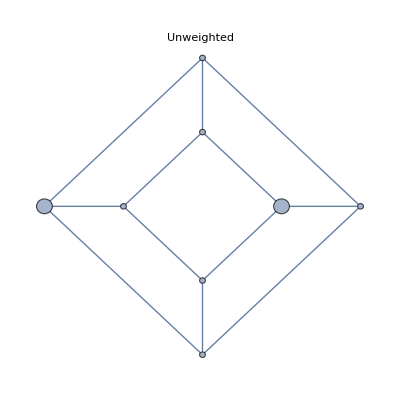
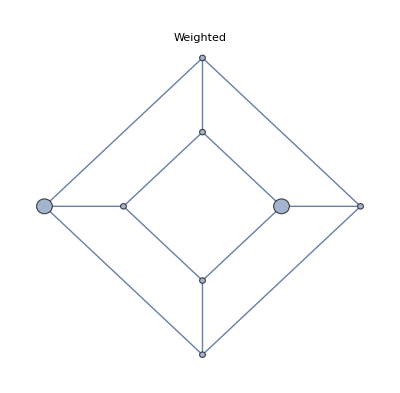

```mathematica
{PetersenGraph[4,1,VertexSize->{1->Medium,7->Medium},PlotLabel->"Unweighted"],PetersenGraph[4,1,EdgeWeight->{4,0,3,1,3,2,7,8,5,2,1,6},VertexSize->{1->Medium,7->Medium},PlotLabel->"Weighted"]}
```

```mathematica
Table[GraphDistance[g,1,7],{g,}]
```

{3,7.}

“UnitWeight” method will the weight 1 for every edge:

```mathematica
GridGraph[{2,3},EdgeWeight->{5,2,2,5,1,2,2},VertexSize->{1->Small,5->Small}]
```

-Graphics-

```mathematica
GraphDistance[,1,5,Method->"UnitWeight"]
```

2

“Dijkstra” can be used for graphs with positive edge weights only:

```mathematica
GridGraph[{2,3},EdgeWeight->{2,5,2,1,5,2,2},VertexSize->{1->Small,5->Small}]
```

-Graphics-

```mathematica
GraphDistance[,1,5,Method->"Dijkstra"]
```

8.

“BellmanFord” can be used for directed graphs, including negative edge weights:

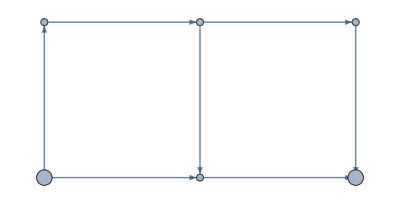

```mathematica
WeightedAdjacencyGraph[({{∞, 2, 5, ∞, ∞, ∞}, {∞, ∞, ∞, 2, ∞, ∞}, {∞, ∞, ∞, ∞, 5, ∞}, {∞, ∞, -2, ∞, ∞, 2}, {∞, ∞, ∞, ∞, ∞, ∞}, {∞, ∞, ∞, ∞, 2, ∞}}),VertexSize->{1->Small,5->Small},AbsoluteOptions[GridGraph[{2,3}],VertexCoordinates]]
```

```mathematica
GraphDistance[,1,5,Method->"BellmanFord"]
```

7.

## Properties & Relations

The distance between two vertices can be found using FindShortestPath:

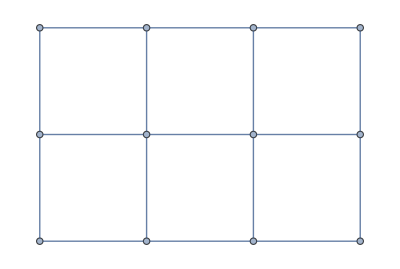

```mathematica
g=GridGraph[{3,4}]
```

```mathematica
FindShortestPath[g,1,12]
```

{1,2,3,6,9,12}

```mathematica
Length[FindShortestPath[g,1,12]]-1
```

5

```mathematica
GraphDistance[g,1,12]
```

5

Distance matrix:

```mathematica
GraphDistanceMatrix[g][[1,12]]
```

5

```mathematica
CountryData["UnitedStates","BorderingCountries"]
```

{Canada,Mexico}

```mathematica
UndirectedEdge[CountryData@"UnitedStates",#]&/@CountryData["UnitedStates","BorderingCountries"]
```

{United States<->Canada,United States<->Mexico}

```mathematica
(country↦UndirectedEdge[CountryData@country,#]&/@CountryData[country,"BorderingCountries"])/@CountryData[]
```

```mathematica
Flatten[(country↦UndirectedEdge[CountryData@country,#]&/@CountryData[country,"BorderingCountries"])/@CountryData[][[;;10]]]
```

{Afghanistan<->China,Afghanistan<->Iran,Afghanistan<->Pakistan,Afghanistan<->Tajikistan,Afghanistan<->Turkmenistan,Afghanistan<->Uzbekistan,Albania<->Greece,Albania<->Kosovo,Albania<->North Macedonia,Albania<->Montenegro,Algeria<->Libya,Algeria<->Mali,Algeria<->Mauritania,Algeria<->Morocco,Algeria<->Niger,Algeria<->Tunisia,Algeria<->Western Sahara,Andorra<->France,Andorra<->Spain,Angola<->Democratic Republic of the Congo,Angola<->Namibia,Angola<->Republic of the Congo,Angola<->Zambia,Argentina<->Bolivia,Argentina<->Brazil,Argentina<->Chile,Argentina<->Paraguay,Argentina<->Uruguay}

```mathematica
Union[Flatten[(country↦UndirectedEdge[CountryData@country,#]&/@CountryData[country,"BorderingCountries"])/@CountryData[][[;;50]]]]
```

{Afghanistan<->China,Afghanistan<->Iran,Afghanistan<->Pakistan,Afghanistan<->Tajikistan,Afghanistan<->Turkmenistan,Afghanistan<->Uzbekistan,Albania<->Greece,Albania<->Kosovo,Albania<->North Macedonia,Albania<->Montenegro,Algeria<->Libya,Algeria<->Mali,Algeria<->Mauritania,Algeria<->Morocco,Algeria<->Niger,Algeria<->Tunisia,Algeria<->Western Sahara,Andorra<->France,Andorra<->Spain,Angola<->Democratic Republic of the Congo,Angola<->Namibia,Angola<->Republic of the Congo,Angola<->Zambia,Argentina<->Bolivia,Argentina<->Brazil,Argentina<->Chile,Argentina<->Paraguay,Argentina<->Uruguay,Armenia<->Azerbaijan,Armenia<->Georgia,Armenia<->Iran,Armenia<->Turkey,Austria<->Czech Republic,Austria<->Germany,Austria<->Hungary,Austria<->Italy,Austria<->Liechtenstein,Austria<->Slovakia,Austria<->Slovenia,Austria<->Switzerland,Azerbaijan<->Armenia,Azerbaijan<->Georgia,Azerbaijan<->Iran,Azerbaijan<->Russia,Azerbaijan<->Turkey,Bangladesh<->India,Bangladesh<->Myanmar,Belarus<->Latvia,Belarus<->Lithuania,Belarus<->Poland,Belarus<->Russia,Belarus<->Ukraine,Belgium<->France,Belgium<->Germany,Belgium<->Luxembourg,Belgium<->Netherlands,Belize<->Guatemala,Belize<->Mexico,Benin<->Burkina Faso,Benin<->Niger,Benin<->Nigeria,Benin<->Togo,Bhutan<->China,Bhutan<->India,Bolivia<->Argentina,Bolivia<->Brazil,Bolivia<->Chile,Bolivia<->Paraguay,Bolivia<->Peru,Bosnia and Herzegovina<->Croatia,Bosnia and Herzegovina<->Montenegro,Bosnia and Herzegovina<->Serbia,Botswana<->Namibia,Botswana<->South Africa,Botswana<->Zambia,Botswana<->Zimbabwe,Brazil<->Argentina,Brazil<->Bolivia,Brazil<->Colombia,Brazil<->French Guiana,Brazil<->Guyana,Brazil<->Paraguay,Brazil<->Peru,Brazil<->Suriname,Brazil<->Uruguay,Brazil<->Venezuela,Brunei<->Malaysia,Bulgaria<->Greece,Bulgaria<->North Macedonia,Bulgaria<->Romania,Bulgaria<->Serbia,Bulgaria<->Turkey,Burkina Faso<->Benin,Burkina Faso<->Ghana,Burkina Faso<->Ivory Coast,Burkina Faso<->Mali,Burkina Faso<->Niger,Burkina Faso<->Togo,Burundi<->Democratic Republic of the Congo,Burundi<->Rwanda,Burundi<->Tanzania,Cambodia<->Laos,Cambodia<->Thailand,Cambodia<->Vietnam,Cameroon<->Central African Republic,Cameroon<->Chad,Cameroon<->Equatorial Guinea,Cameroon<->Gabon,Cameroon<->Nigeria,Cameroon<->Republic of the Congo,Canada<->United States,Central African Republic<->Cameroon,Central African Republic<->Chad,Central African Republic<->Democratic Republic of the Congo,Central African Republic<->Republic of the Congo,Central African Republic<->South Sudan,Central African Republic<->Sudan,Chad<->Cameroon,Chad<->Central African Republic,Chad<->Libya,Chad<->Niger,Chad<->Nigeria,Chad<->Sudan,Chile<->Argentina,Chile<->Bolivia,Chile<->Peru,China<->Afghanistan,China<->Bhutan,China<->India,China<->Kazakhstan,China<->Kyrgyzstan,China<->Laos,China<->Mongolia,China<->Myanmar,China<->Nepal,China<->North Korea,China<->Pakistan,China<->Russia,China<->Tajikistan,China<->Vietnam,Colombia<->Brazil,Colombia<->Ecuador,Colombia<->Panama,Colombia<->Peru,Colombia<->Venezuela}

```mathematica
Graph[%231]
```

-Graphics-

```mathematica
Graph[DeleteMissing@Union@Flatten[(country↦UndirectedEdge[CountryData@country,#]&/@CountryData[country,"BorderingCountries"])/@DeleteMissing@CountryData[]]]
```

-Graphics-

Country chains Wolfram Challenge

```mathematica
countryGraph=Graph[DeleteMissing@Union@Flatten[(country↦UndirectedEdge[CountryData@country,#]&/@CountryData[country,"BorderingCountries"])/@DeleteMissing@CountryData[]]]
```

-Graphics-

```mathematica
GraphDistance[countryGraph,CountryData@"China",]
```

1

```mathematica
GraphDistance[countryGraph,CountryData@"Ethiopia",]
```

7

In a connected graph,  the VertexEccentivity can be computed using GraphDistance:

```mathematica
g=GridGraph[{3,4}]
```

-Graphics-

```mathematica
GraphDistance[g,1,#]&/@VertexList[g]
```

{0,1,2,1,2,3,2,3,4,3,4,5}

The distance between two vertices belonging to different connected components is Infinity:

```mathematica
g=-Graphics-;
```

```mathematica
ConnectedGraphQ[g]
```

False

```mathematica
ConnectedComponents[g]
```

{{1,2,3},{4,5}}

```mathematica
GraphDistance[g,3,5]
```

∞

## GraphDistanceMatrix:

```mathematica
GraphDistanceMatrix[PetersenGraph[]]//MatrixForm
```

(0 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2
2 | 0 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 2
1 | 2 | 0 | 2 | 1 | 2 | 2 | 1 | 2 | 2
1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 1 | 2
2 | 1 | 1 | 2 | 0 | 2 | 2 | 2 | 2 | 1
1 | 2 | 2 | 2 | 2 | 0 | 1 | 2 | 2 | 1
2 | 1 | 2 | 2 | 2 | 1 | 0 | 1 | 2 | 2
2 | 2 | 1 | 2 | 2 | 2 | 1 | 0 | 1 | 2
2 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 0 | 1
2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 1 | 0)

## Properties and relations:

Rows and columns of the distance matrix follow the same order given by VertexList:

```mathematica
g=-Graphics-;
```

```mathematica
VertexList[g]
```

{2,3,1,4}